```mathematica
Clear[β, n, n1,n2, ϵ, δ, E02, E01]
```

```mathematica
(*assume n1 > n2 *) 
Reduce[δ-2*n1/n-ϵ(E02-E01) > δ-(2*n2/n)-ϵ(E01-E02)&&β>1&&n>1&&n1>n2&&n2>1, ϵ]
Reduce[δ-2*n1/n-ϵ(E02-E01) > ϵ(E02-E01)-2*n2/n+δ&&β>1&&n>1&&n1>n2&&n2>1, ϵ]
```

δ∈ℝ&&E02∈ℝ&&n1>1&&1<n2<n1&&n>1&&((E01<E02&&β>1&&ϵ<(n1-n2)/(E01 n-E02 n))||(E01>E02&&β>1&&ϵ>(n1-n2)/(E01 n-E02 n)))

δ∈ℝ&&E02∈ℝ&&n1>1&&1<n2<n1&&n>1&&((E01<E02&&β>1&&ϵ<(n1-n2)/(E01 n-E02 n))||(E01>E02&&β>1&&ϵ>(n1-n2)/(E01 n-E02 n)))

```mathematica
E01 = (n1 / n) + n1 *  1/( β(n1-1)+(n-n1))
E02 = (n2 / n) + n2 *  1/( β(n2-1)+(n-n2))
```

n1/n+n1/(n-n1+(-1+n1) β)

n2/n+n2/(n-n2+(-1+n2) β)

```mathematica
(*assume n1 > n2 *)
```

δ∈ℝ&&(E02|n2)∈ℝ&&n1>n2&&((E01<E02&&n>1&&β>1&&ϵ<(n1-n2)/(E01 n-E02 n))||(E01>E02&&n>1&&β>1&&ϵ>(n1-n2)/(E01 n-E02 n)))

```mathematica
(*assume n1 > n2 *) 
Reduce[δ-2*n1/n-ϵ(E02-E01) > ϵ(E02-E01)-2*n2/n+δ&&β>1&&n>1&&n1>n2&&n≥n2≥0&&n≥n1≥0, ϵ]
```

δ∈ℝ&&((1<n<3/2&&((1<β<n&&0≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(β==n&&(-n+β)/(-1+β)<n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n<β<n/(2 (-1+n)^2)-1/2 √((-3 n^2+8 n^3-4 n^4)/(-1+n)^4)&&((0≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1<n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)<n2<(-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(n/(2 (-1+n)^2)-1/2 √((-3 n^2+8 n^3-4 n^4)/(-1+n)^4)≤β<2 n&&((0≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<n&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(β==2 n&&(((-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<n&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(2 n<β≤n/(2 (-1+n)^2)+1/2 √((-3 n^2+8 n^3-4 n^4)/(-1+n)^4)&&((0≤n2<(-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<n&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(β>n/(2 (-1+n)^2)+1/2 √((-3 n^2+8 n^3-4 n^4)/(-1+n)^4)&&((0≤n2<(-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1<n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)<n2<(-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))))||(n==3/2&&((1<β<3/2&&0≤n2<3/2&&n2<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(β==3/2&&0<n2<3/2&&n2<n1≤3/2&&ϵ>1)||(3/2<β<3&&((0≤n2<(-3/2+β)/(-1+β)&&((n2<n1<(-3/2+β)/(-1+β)&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-3/2+β)/(-1+β)<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-3/2+β)/(-1+β)<n2<(-9/4+(3 β)/4+β^2/2)/(-β/2+β^2/2)&&n2<n1≤3/2&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-9/4+(3 β)/4+β^2/2)/(-β/2+β^2/2)&&n2<n1<3/2&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-9/4+(3 β)/4+β^2/2)/(-β/2+β^2/2)<n2<(-3/2+β)/(-1+β)+√((-9/4+(3 β)/2)/(-1+β)^2)&&((n2<n1<(-9/2+(3 n2)/2+(9 β)/2-(5 n2 β)/2-β^2+n2 β^2)/(-3/2+n2+(5 β)/2-2 n2 β-β^2+n2 β^2)&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-9/2+(3 n2)/2+(9 β)/2-(5 n2 β)/2-β^2+n2 β^2)/(-3/2+n2+(5 β)/2-2 n2 β-β^2+n2 β^2)<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-3/2+β)/(-1+β)+√((-9/4+(3 β)/2)/(-1+β)^2)≤n2<3/2&&n2<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(β==3&&((0≤n2<3/4&&((n2<n1<3/4&&ϵ<(9/4-3 n1-3 n2+4 n1 n2)/(-3 n1-3 n2+4 n1 n2))||(3/4<n1≤3/2&&ϵ>(9/4-3 n1-3 n2+4 n1 n2)/(-3 n1-3 n2+4 n1 n2))))||(3/4<n2<3/2&&n2<n1≤3/2&&ϵ<(9/4-3 n1-3 n2+4 n1 n2)/(-3 n1-3 n2+4 n1 n2))))||(β>3&&((0≤n2<(-3/2+β)/(-1+β)-√((-9/4+(3 β)/2)/(-1+β)^2)&&((n2<n1<(-9/2+(3 n2)/2+(9 β)/2-(5 n2 β)/2-β^2+n2 β^2)/(-3/2+n2+(5 β)/2-2 n2 β-β^2+n2 β^2)&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-9/2+(3 n2)/2+(9 β)/2-(5 n2 β)/2-β^2+n2 β^2)/(-3/2+n2+(5 β)/2-2 n2 β-β^2+n2 β^2)<n1<(-3/2+β)/(-1+β)&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-3/2+β)/(-1+β)<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-3/2+β)/(-1+β)-√((-9/4+(3 β)/2)/(-1+β)^2)≤n2<(-3/2+β)/(-1+β)&&((n2<n1<(-3/2+β)/(-1+β)&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-3/2+β)/(-1+β)<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-3/2+β)/(-1+β)<n2<(-9/4+(3 β)/4+β^2/2)/(-β/2+β^2/2)&&n2<n1≤3/2&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-9/4+(3 β)/4+β^2/2)/(-β/2+β^2/2)&&n2<n1<3/2&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-9/4+(3 β)/4+β^2/2)/(-β/2+β^2/2)<n2<(-3/2+β)/(-1+β)+√((-9/4+(3 β)/2)/(-1+β)^2)&&((n2<n1<(-9/2+(3 n2)/2+(9 β)/2-(5 n2 β)/2-β^2+n2 β^2)/(-3/2+n2+(5 β)/2-2 n2 β-β^2+n2 β^2)&&ϵ<(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-9/2+(3 n2)/2+(9 β)/2-(5 n2 β)/2-β^2+n2 β^2)/(-3/2+n2+(5 β)/2-2 n2 β-β^2+n2 β^2)<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-3/2+β)/(-1+β)+√((-9/4+(3 β)/2)/(-1+β)^2)≤n2<3/2&&n2<n1≤3/2&&ϵ>(9/4-(3 n1)/2-(3 n2)/2+n1 n2-3 β+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(9/2-(3 n1)/2-(3 n2)/2+n1 n2-(9 β)/2+(5 n1 β)/2+(5 n2 β)/2-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))))||(n>3/2&&((1<β<n&&0≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(β==n&&(-n+β)/(-1+β)<n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n<β<2 n&&((0≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1<n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)<n2<(-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(β==2 n&&(((-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)<n2<(-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||(β>2 n&&((0≤n2<(-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)-√((-n^2+n β)/(-1+β)^2)≤n2<(-n+β)/(-1+β)&&((n2<n1<(-n+β)/(-1+β)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n+β)/(-1+β)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)<n2<(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1≤n&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||(n2==(-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)&&n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-n^2+2 n β-n^2 β-β^2+n β^2)/(β-n β-β^2+n β^2)<n2<(-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)&&((n2<n1<(-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)&&ϵ<(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))||((-2 n^2+n n2+3 n β-n2 β-n n2 β-β^2+n2 β^2)/(-n+n2+β+n β-2 n2 β-β^2+n2 β^2)<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2))))||((-n+β)/(-1+β)+√((-n^2+n β)/(-1+β)^2)≤n2<n&&n2<n1≤n&&ϵ>(n^2-n n1-n n2+n1 n2-2 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)/(2 n^2-n n1-n n2+n1 n2-3 n β+n1 β+n n1 β+n2 β+n n2 β-2 n1 n2 β+β^2-n1 β^2-n2 β^2+n1 n2 β^2)))))))

80

0.8

33.

31.

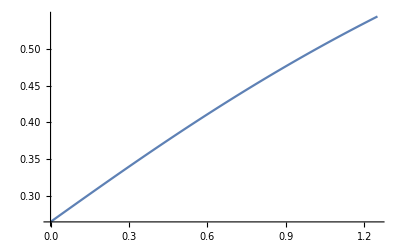

```mathematica
n=80
δ=0.8
n1=δ/2*n+1
n2 =δ/2*n-1
Plot[(n1-n2)/(n*(E01-E02)),{β, 0, 1.25}]
```